```mathematica
y[x_]:=1-0.3 x+0.04 x^2-4.5*x^3+0.4 x^4+20 RandomReal[{-1,1}];
```

```mathematica
mydata=Table[{x,y[x]},{x,0,20}]
```

{{0,14.7317},{1,1.58424},{2,-10.2966},{3,-93.3567},{4,-204.323},{5,-292.639},{6,-459.802},{7,-588.767},{8,-645.683},{9,-653.864},{10,-515.15},{11,-117.41},{12,532.844},{13,1555.06},{14,3013.64},{15,5048.82},{16,7775.63},{17,11287.5},{18,15738.4},{19,21292.5},{20,28018.1}}

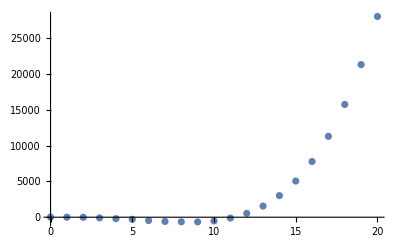

```mathematica
dataplot=ListPlot[mydata]
```

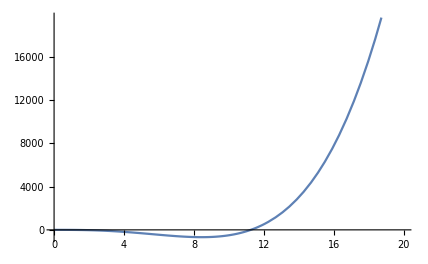

```mathematica
p[x_]:=1-0.3 x+0.04 x^2-4.5*x^3+0.4 x^4;
Plot[p[x],{x,0,20}]
```

```mathematica
fitdata=Fit[mydata,{1,x,x^2,x^3,x^4},x]
```

19.3178-14.5761 x+3.30497 x^2-4.76605 x^3+0.406896 x^4

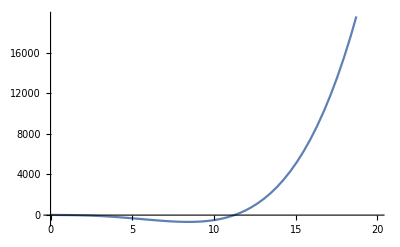

```mathematica
fitplot=Plot[fitdata,{x,0,20}]
```

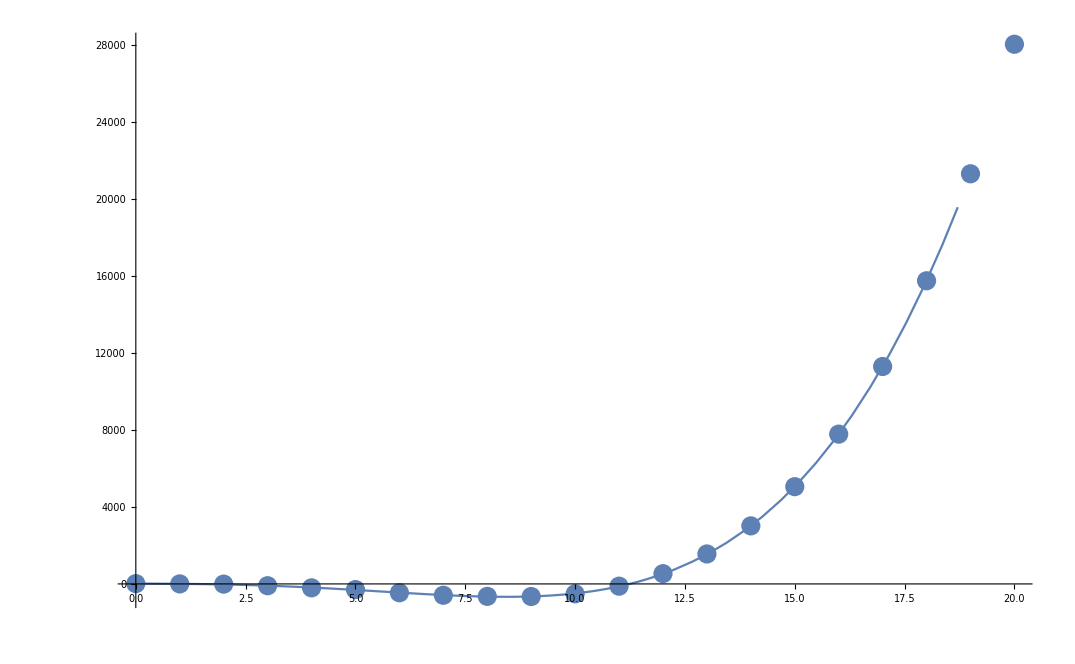

```mathematica
Show[dataplot,fitplot]
```

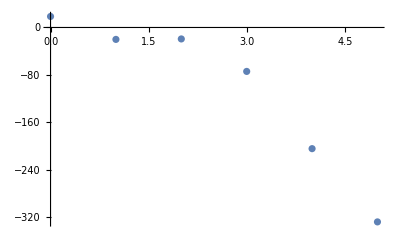

```mathematica
mydata2=Table[{x,y[x]},{x,0,5}];
dataplot2=ListPlot[mydata2]
```

```mathematica
fitdata2=Fit[mydata2,{1,x,x^2,x^3,x^4},x]
```

18.7253-116.229 x+112.189 x^2-39.0619 x^3+3.69893 x^4

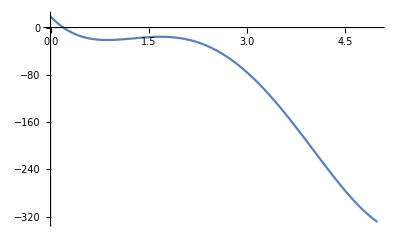

```mathematica
fitplot2=Plot[fitdata2,{x,0,5}]
```

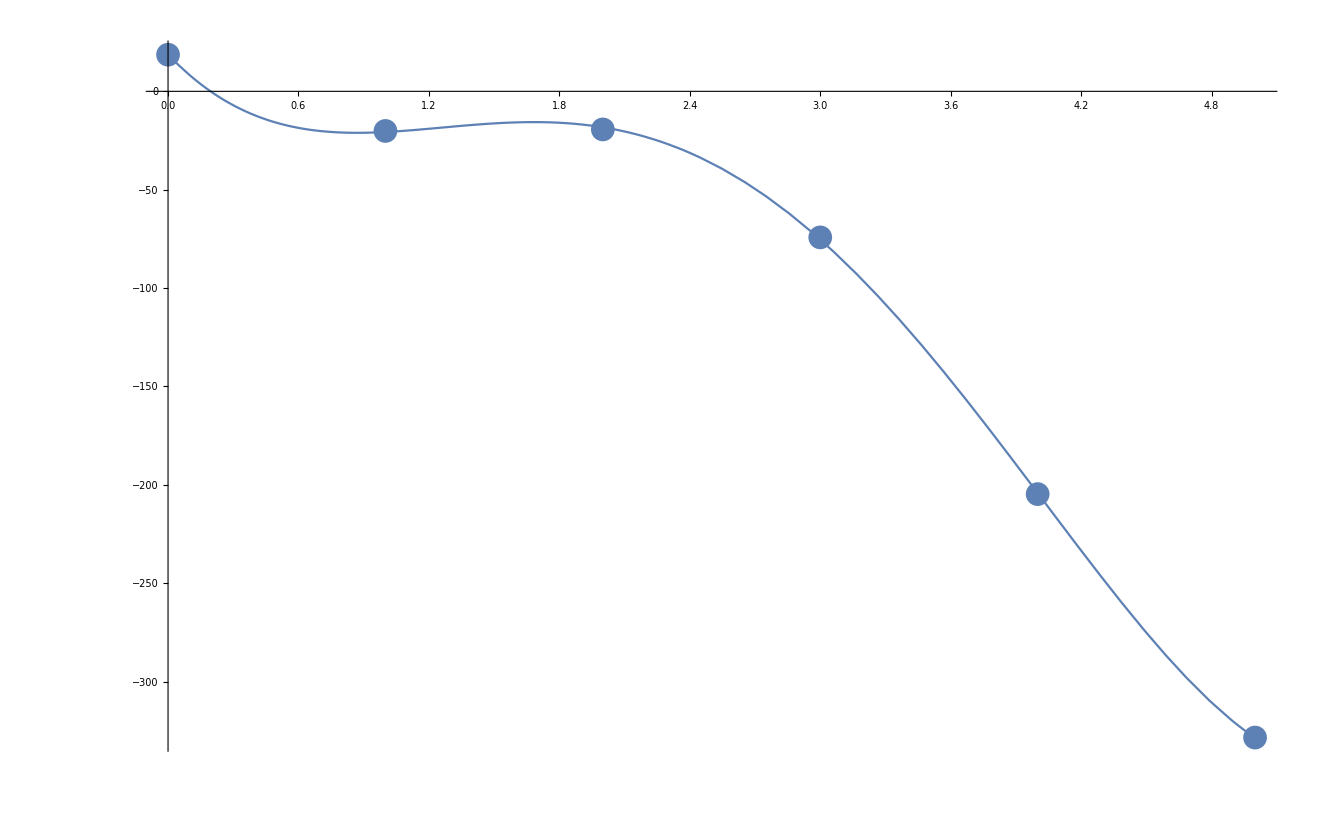

```mathematica
Show[dataplot2,fitplot2]
```

```mathematica
y2[x_]:=1-0.3 x+0.04 x^2-4.5*x^3+0.4 x^4+100 RandomReal[{-1,1}];
```

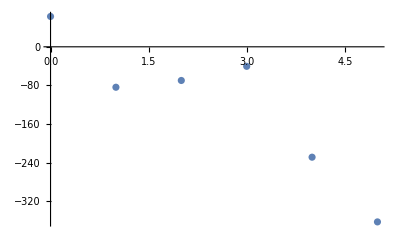

```mathematica
mydata3=Table[{x,y2[x]},{x,0,5}];
dataplot3=ListPlot[mydata3]
```

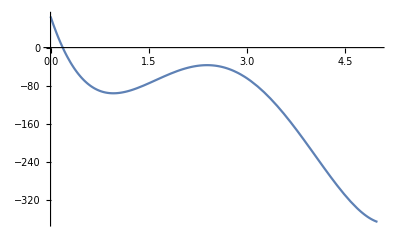

```mathematica
fitdata3=Fit[mydata3,{1,x,x^2,x^3,x^4},x];
fitplot3=Plot[fitdata3,{x,0,5}]
```

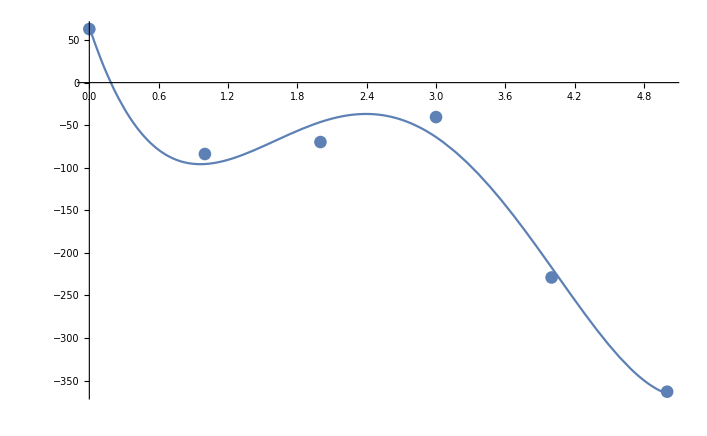

```mathematica
Show[dataplot3,fitplot3]
```

```mathematica
webdata=Import["https://eee.uci.edu/12f/40330/lesson3.dat"]
```

{{0.,0.01},{1000.,0.00625},{1800.,0.00476},{2800.,0.0037},{3600.,0.00313},{4400.,0.0027},{5200.,0.00241},{6200.,0.00208}}

```mathematica
datdata=Import["F:/lesson3.dat"]
```

{{0.,0.01},{1000.,0.00625},{1800.,0.00476},{2800.,0.0037},{3600.,0.00313},{4400.,0.0027},{5200.,0.00241},{6200.,0.00208}}

```mathematica
datdata2=webdata;
```

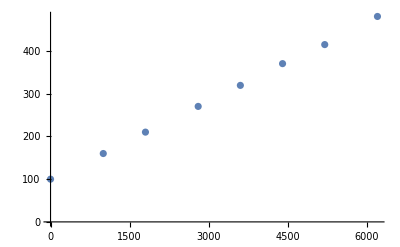

```mathematica
datdata2[[All,2]]=1/webdata[[All,2]];
ListPlot[datdata2]
```

```mathematica
fitdata=Fit[datdata2,{1,x},x]
```

99.3685+0.0612389 x

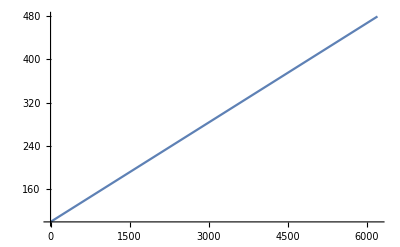

```mathematica
fitplot=Plot[fitdata,{x,0,6200}]
```

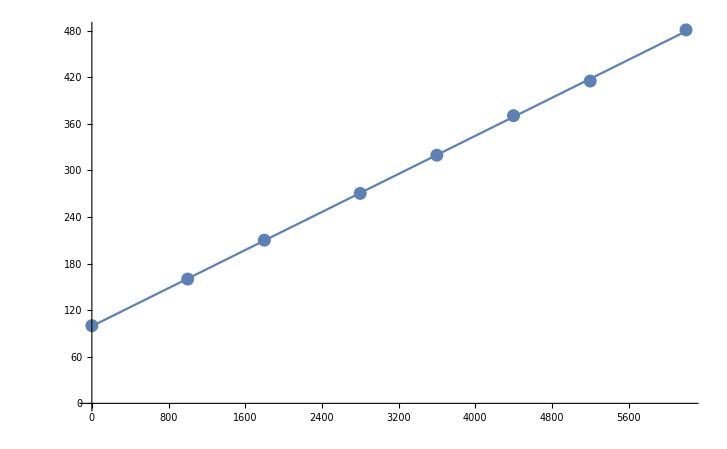

```mathematica
Show[ListPlot[datdata2],fitplot]
```